# Bitcoin-USD Movements

This notebook serves to analyze Bitcoin price movements on either a daily, weekly, or monthly basis .

```mathematica
(* Buttons to hide / show code *)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
(* Since Mathematica operates in a global environment, let's clear all that, so we're clean *)
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
(* The earliest date for data *)
origindate="Sep. 14, 2011";

(* Put these stats in the summary boxes placed within each plot *)
bstats[lst_]:=Return[<|
count->Length[lst]
,min->Min[lst]
,mean->Mean[lst]
,median-> Median[lst]
,max->Max[lst]
,std->StandardDeviation[lst]
|>//Dataset];

(* Time increment strings for selection *)
ly[str_]:=Switch[str,"Day","Daily","Week","Weekly","Month","Monthly","Year","Yearly"];

(* Default properties for generated plots *)
imagesize=1250;
labelstyle=Directive[14];
titlestyle={20,Red};
imagemargins=20;
plotbackground=Lighter[LightGray,0.75];
ticks2={#,ToString[Quantity[100 #,"Percent"],StandardForm]}&/@Range[-1,1,1/10];
```

```mathematica
(* Here we fetch the data, and normalize it from a Dataset to a plain list *)
btcDataFull = FinancialData["BTC/USD", origindate]//Normal;
(* How many days data have we got? *)
days = btcDataFull//Length;

(* How much of the list do we take for display? *)
takes=MapIndexed[
#1->Style[ToString[First[#2]]<> " yr",16]&
,Join[
Range[365,days,365]
,{days}
]
]//ReverseSort;
```

```mathematica
(* The real fun begins here *)
Manipulate[
(* insetscale places some of the inset stat boxes horizontally *)
insetscale={.07,.875};
intervally=ly[interval];
btcData=TimeSeriesAggregate[Take[btcDataFull,-since],interval,Last];
labelstyle={18};
updatedstr=Style[StringForm["(updated: ``)" , DateString[]],15];

(* A B S O L U T E   C H A N G E S *)
absolutechanges = Table[Last[btcData[[n]]]-Last[btcData[[n-1]]],{n,2, Length@btcData}];
tsabsolutechanges= TimeSeries[Table[{First[btcData[[n]]],Last[btcData[[n]]]-Last[btcData[[n-1]]]},{n,2, Length@btcData}]];
dlpabsolute=DateListPlot[
tsabsolutechanges
,PlotLabel->Column[
{
Style[
StringForm["Absolute `` Price Changes (USD)",intervally]
,titlestyle
]
,StringForm[
"`` ``s"
,Length[tsabsolutechanges["Values"]]
,interval
]
,updatedstr
}
,Center
]
,ImageSize->imagesize
,ImageMargins->20
,PlotRange->Full
,FrameTicks->All
, GridLines->Automatic
, Joined->False
,FrameLabel->{{HoldForm[US Dollars],None},{None,None}}
,LabelStyle->labelstyle
,ImageMargins->imagemargins
,Background->plotbackground
,Epilog->
Inset[
Framed[bstats[absolutechanges]]
,Scaled[insetscale]
,Background->White
]
];
filename = StringForm["BTC-USD-Movements-Absolute-``.jpg",intervally]//ToString;
Export[filename, dlpabsolute];
rankabs=SortBy[tsabsolutechanges//Normal,Last];
worstabs=Take[rankabs,Min[100,Length[rankabs]]]//Dataset;
bestabs=ReverseSortBy[Take[rankabs,Max[-100,-Length[rankabs]]],#[[2]]&]//Dataset;
worstandbestabs=Column[{
Style[
StringForm["Worst and Best ``s (Absolute Dollars)", interval]
,titlestyle
]
,updatedstr
,Row[{worstabs,bestabs}
,ImageSize->600
, Alignment->Center
]
}
,Alignment->Center
, Frame->True
];

(* R E L A T I V E   C H A N G E S *)
relativechanges = Table[
{
First[btcData[[n]]],(Last[btcData[[n]]]-Last[btcData[[n-1]]])/(Mean[{Last[btcData[[n]]],Last[btcData[[n-1]]]}])
}
,{n,2, Length@btcData}
];
tsrelativechanges = TimeSeries[relativechanges];
dlprelative=DateListPlot[
tsrelativechanges
,PlotLabel->Column[
{
Style[
StringForm["Relative `` Changes",intervally]
,titlestyle
]
,StringForm[
"`` ``s"
,Length[tsrelativechanges["Values"]]
,interval
]
,updatedstr
}
,Center
]
,PlotRange->All
,GridLines->{DateRange[{2011},{2030},"Year"],Range[-1,1,1/10]}
,Ticks->{Automatic,ticks2}
,FrameTicks->All
,Joined->False
,PlotMarkers->{Automatic,Scaled[0.005]}
,Filling->Axis
,FillingStyle->{Red, Green}
,Background->plotbackground
,ImageSize->imagesize
,LabelStyle-> labelstyle
,ImageMargins->imagemargins
,Epilog->
Inset[
Framed[bstats[tsrelativechanges["Values"]]]
,Scaled[insetscale]
,Background->White
]
];
filename = StringForm["BTC-USD-Movements-Relative-``.jpg",intervally]//ToString;
Export[filename, dlprelative];
rankrel=SortBy[tsrelativechanges//Normal,Last];
worstrel={#[[1]],#[[2]]//PercentForm}&/@Take[rankrel,Min[100,Length[rankrel]]]//Dataset;
bestrel=({#[[1]],#[[2]]//PercentForm}&/@ReverseSortBy[Take[rankrel,Max[-100,-Length[rankrel]]],#[[2]]&])//Dataset;
worstandbestrel=Column[{
Style[
StringForm["Worst and Best ``s (Relative)", interval]
,titlestyle
]
,updatedstr
,Row[{worstrel,bestrel}
,ImageSize->600
, Alignment->Center
]
}
,Alignment->Center
, Frame->True
];
positives=Select[tsrelativechanges["Values"],#>0& ];
negatives=Select[tsrelativechanges["Values"],#<0& ];
mhistpositive=Histogram[
positives
,25
,PlotLabel->Column[
{
Style[
StringForm["Relative `` Positive Price Movements",intervally]
,titlestyle
]
,StringForm[
"`` of `` ``s"
,Length[positives]
,Length[positives] +Length[ negatives]
,interval
]
,updatedstr
}
,Center
]
,LabelStyle->labelstyle
,PlotRange->Full
,ImageSize->imagesize
,ImageMargins->imagemargins
,GridLines->Automatic
,Ticks->{ticks2, Automatic}
,FrameTicks->All
,ChartStyle->Green
,LabelingFunction->Above
,Background->plotbackground
,Epilog->Inset[
Framed[bstats[positives]]
,Scaled[{.50,.85}]
,Background->White
]
];
mhistnegative=Histogram[
{negatives}
,50
,PlotLabel->Column[
{
Style[
StringForm["Relative `` Negative Price Movements",intervally]
,titlestyle
]
,StringForm[
"`` of `` ``s"
,Length[negatives]
,Length[positives] +Length[ negatives]
,interval
]
,updatedstr
}
,Center
]
,LabelStyle->labelstyle
,PlotRange->Full
,ImageSize->imagesize
,ImageMargins->imagemargins
,GridLines->Automatic
,Ticks->{ticks2, Automatic}
,FrameTicks->All
,ChartStyle->Red
,LabelingFunction->Above
,LabelingFunction->Above
,Background->plotbackground
,Epilog->Inset[
Framed[bstats[negatives]]
,Scaled[{.50,.85}]
,Background->White
]
];
mhistcombined=Manipulate[
Histogram[{
positives,negatives}
,x
,PlotLabel->Column[
{
Style[
StringForm["Relative `` Movements",intervally]
,titlestyle
]
,StringForm[
"`` ``s"
,Length[positives] +Length[ negatives]
,interval
]
,updatedstr
}
,Center
]
,LabelStyle->labelstyle
,PlotRange->Full
,ImageSize->imagesize
,ImageMargins->imagemargins
,GridLines->{Range[-1,1,1/10],Automatic}
,Ticks->{ticks2, Automatic}
,FrameTicks->All
,ChartStyle->{Green, Red}
,LabelStyle->If[x>75,labelstyle,{labelstyle,Directive[If[x<50,12,8]]}]
,LabelingFunction->If[x>75,None,Above]
,Background->plotbackground
,Epilog->{
Inset[
Framed[bstats[Join[positives,negatives]]]
,Scaled[{.30,.90}]
,Background->White
]
,Inset[
Framed[bstats[negatives]]
,Scaled[{.10,.40}]
,Background->White
]
,Inset[
Framed[bstats[positives]]
,Scaled[{.90,.40}]
,Background->White
]
}
]
,{{x,50,Style["Bins: ",{15}]},Range[10,200,10]}
];
Column[{
Style[
StringForm["Absolute `` Movements",intervally]
,"Section"
]
,dlpabsolute
,worstandbestabs
,Spacer[10]
,Style[
StringForm["Relative `` Movements",intervally]
,"Section"
]
,dlprelative
,worstandbestrel
,mhistpositive
,mhistnegative
,mhistcombined
}
],
{
{interval,"Day"}
,#->Style[#,16]&/@{"Day", "Week","Month"}
}
, {
{since,days}
, takes
}
]
```

## Starting here to quantify price volatility (not ready for prime time yet)

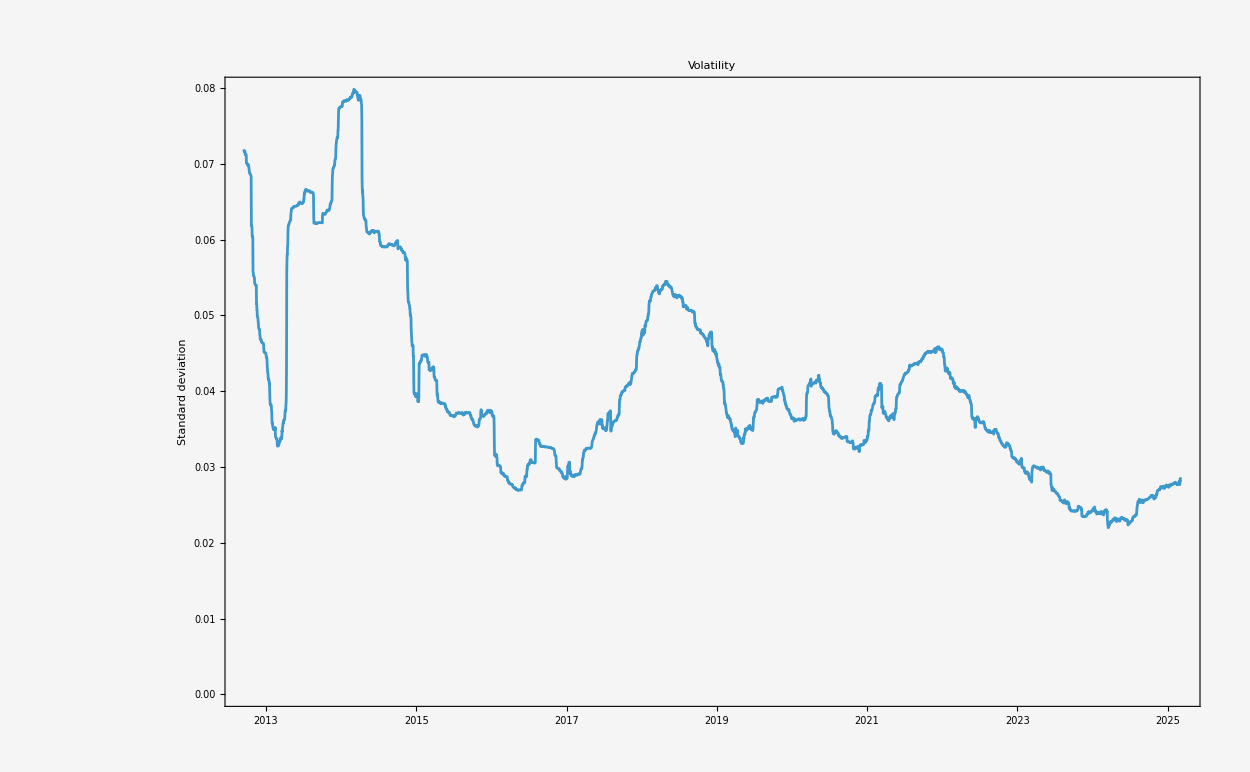

```mathematica
relativechangesall = Table[
{
First[btcDataFull[[n]]]
,(Last[btcDataFull[[n]]]-Last[btcDataFull[[n-1]]])/Mean[{Last[btcDataFull[[n]]],Last[btcDataFull[[n-1]]]}]
}
,{n,2, Length@btcDataFull}
];
tsrelativechangesall = TimeSeries[relativechangesall];
annualvolatility=MovingMap[StandardDeviation,tsrelativechangesall,Quantity[12,"Months"]];
DateListPlot[
annualvolatility
,PlotLabel->"Volatility"
,ImageSize->imagesize
,ImageMargins->20
,ImageMargins->imagemargins
,Background->plotbackground
,PlotRange->Full
,FrameTicks->All
,GridLines->{Automatic,Range[0,0.2,0.01]}
,FrameLabel->{{HoldForm[Standard deviation],None},{None,None}}
,LabelStyle->labelstyle
]
```

```mathematica
{#[[1]],#[[2]]//PercentForm}&/@Take[rankrel,Min[100,Length[rankrel]]]
```

{{Fri 12 Apr 2013 12:00:00GMT-5,-64.06%},{Fri 21 Oct 2011 12:00:00GMT-5,-54.55%},{Mon 20 Aug 2012 12:00:00GMT-5,-35.51%},{Thu 11 Apr 2013 12:00:00GMT-5,-34.27%},{Thu 15 Jan 2015 12:00:00GMT-5,-31.02%},{Tue 15 Nov 2011 12:00:00GMT-5,-30.24%},{Thu 19 Dec 2013 12:00:00GMT-5,-25.74%},{Tue 27 Sep 2011 12:00:00GMT-5,-23.04%},{Thu 12 Mar 2020 12:00:00GMT-5,-22.77%},{Sat 7 Dec 2013 12:00:00GMT-5,-22.73%},{Wed 20 Nov 2013 12:00:00GMT-5,-22.07%},{Tue 17 Dec 2013 12:00:00GMT-5,-22.02%},{Wed 3 Aug 2016 12:00:00GMT-5,-21.79%},{Tue 16 Apr 2013 12:00:00GMT-5,-20.73%},{Thu 3 Oct 2013 12:00:00GMT-5,-20.31%},{Fri 28 Mar 2014 12:00:00GMT-5,-19.92%},{Fri 11 Apr 2014 12:00:00GMT-5,-19.33%},{Sun 14 Apr 2013 12:00:00GMT-5,-18.12%},{Thu 2 May 2013 12:00:00GMT-5,-18.03%},{Sun 29 Jan 2012 12:00:00GMT-5,-17.98%},{Sat 19 Nov 2011 12:00:00GMT-5,-17.85%},{Wed 17 Jan 2018 12:00:00GMT-5,-17.63%},{Sat 16 Jan 2016 12:00:00GMT-5,-17.59%},{Fri 15 Sep 2017 12:00:00GMT-5,-17.47%},{Tue 6 Feb 2018 12:00:00GMT-5,-17.09%},{Sat 6 Jul 2013 12:00:00GMT-5,-17.04%},{Wed 15 Feb 2012 12:00:00GMT-5,-16.85%},{Sun 6 Nov 2011 12:00:00GMT-5,-16.79%},{Wed 18 Jan 2012 12:00:00GMT-5,-16.79%},{Mon 13 Jun 2022 12:00:00GMT-5,-16.63%},{Fri 13 Mar 2020 12:00:00GMT-5,-16.61%},{Sun 8 Dec 2013 12:00:00GMT-5,-16.13%},{Mon 11 Jan 2021 12:00:00GMT-5,-16.06%},{Tue 20 Nov 2018 12:00:00GMT-5,-15.95%},{Mon 2 Dec 2013 12:00:00GMT-5,-15.86%},{Wed 8 Jan 2014 12:00:00GMT-5,-15.59%},{Fri 28 Jun 2019 12:00:00GMT-5,-14.68%},{Thu 29 Jan 2015 12:00:00GMT-5,-14.47%},{Sun 9 Oct 2011 12:00:00GMT-5,-14.42%},{Sun 23 May 2021 12:00:00GMT-5,-14.24%},{Wed 17 Jul 2019 12:00:00GMT-5,-14.11%},{Wed 14 Jan 2015 12:00:00GMT-5,-14.1%},{Fri 27 Jan 2012 12:00:00GMT-5,-13.72%},{Fri 20 Jan 2012 12:00:00GMT-5,-13.21%},{Sun 10 May 2020 12:00:00GMT-5,-13.17%},{Thu 4 Jul 2013 12:00:00GMT-5,-13.17%},{Wed 11 Nov 2015 12:00:00GMT-5,-13.14%},{Tue 25 Feb 2014 12:00:00GMT-5,-13.02%},{Sun 31 Dec 2017 12:00:00GMT-5,-12.98%},{Sat 4 Dec 2021 12:00:00GMT-5,-12.75%},{Thu 26 Nov 2020 12:00:00GMT-5,-12.73%},{Sun 25 Nov 2018 12:00:00GMT-5,-12.5%},{Thu 13 May 2021 12:00:00GMT-5,-12.13%},{Mon 31 Oct 2011 12:00:00GMT-5,-12.08%},{Fri 6 Jan 2017 12:00:00GMT-5,-12%},{Fri 2 Feb 2018 12:00:00GMT-5,-11.87%},{Sat 3 Dec 2011 12:00:00GMT-5,-11.76%},{Thu 10 Nov 2022 12:00:00GMT-5,-11.73%},{Wed 25 Sep 2019 12:00:00GMT-5,-11.73%},{Mon 5 Feb 2018 12:00:00GMT-5,-11.72%},{Mon 5 Aug 2024 12:00:00GMT-5,-11.64%},{Sat 21 Dec 2013 12:00:00GMT-5,-11.58%},{Fri 12 Jan 2018 12:00:00GMT-5,-11.53%},{Sat 7 Jan 2017 12:00:00GMT-5,-11.27%},{Wed 31 Jan 2018 12:00:00GMT-5,-11.25%},{Fri 30 Mar 2018 12:00:00GMT-5,-11.23%},{Fri 21 Jan 2022 12:00:00GMT-5,-11.13%},{Thu 15 Nov 2018 12:00:00GMT-5,-11.1%},{Tue 23 Feb 2021 12:00:00GMT-5,-11.02%},{Sat 23 Dec 2017 12:00:00GMT-5,-11.02%},{Mon 15 Jul 2019 12:00:00GMT-5,-11%},{Tue 8 Jun 2021 12:00:00GMT-5,-10.98%},{Thu 15 Mar 2018 12:00:00GMT-5,-10.93%},{Wed 22 Jun 2016 12:00:00GMT-5,-10.82%},{Thu 12 Dec 2013 12:00:00GMT-5,-10.78%},{Thu 12 Jan 2017 12:00:00GMT-5,-10.77%},{Sun 19 Mar 2017 12:00:00GMT-5,-10.74%},{Sat 22 Jan 2022 12:00:00GMT-5,-10.66%},{Tue 10 Jan 2012 12:00:00GMT-5,-10.53%},{Sat 23 Jun 2018 12:00:00GMT-5,-10.49%},{Fri 21 Feb 2014 12:00:00GMT-5,-10.43%},{Sat 7 Jan 2012 12:00:00GMT-5,-10.28%},{Thu 21 Nov 2019 12:00:00GMT-5,-10.11%},{Mon 16 Feb 2015 12:00:00GMT-5,-10.08%},{Mon 22 Jan 2018 12:00:00GMT-5,-10.07%},{Thu 19 Mar 2015 12:00:00GMT-5,-10.04%},{Fri 6 Dec 2013 12:00:00GMT-5,-10.03%},{Mon 11 Jun 2018 12:00:00GMT-5,-10.01%},{Thu 21 Jan 2021 12:00:00GMT-5,-9.953%},{Fri 11 Jan 2019 12:00:00GMT-5,-9.935%},{Sun 19 Feb 2012 12:00:00GMT-5,-9.888%},{Mon 1 Jul 2019 12:00:00GMT-5,-9.783%},{Mon 22 Feb 2021 12:00:00GMT-5,-9.733%},{Thu 6 Sep 2018 12:00:00GMT-5,-9.72%},{Fri 15 Jan 2021 12:00:00GMT-5,-9.685%},{Sun 18 Apr 2021 12:00:00GMT-5,-9.678%},{Mon 25 Feb 2019 12:00:00GMT-5,-9.669%},{Sat 25 Mar 2017 12:00:00GMT-5,-9.56%},{Wed 12 Oct 2011 12:00:00GMT-5,-9.524%},{Sun 16 Jul 2017 12:00:00GMT-5,-9.47%}}

```mathematica
StringForm["BTC-USD-Movements-Relative-``.jpg",intervally]//Head
```

StringForm